```mathematica
Solitons from the Korteweg-de Vries Equation 

Som Phene

Introduction
The Korteweg-de Vries Equation (KdV equation) describes the theory of water waves in
shallow channels, such as a canal. It is a non-linear equation which exhibits special
solutions, known as solitons, which are stable and do not disperse with time. Furthermore
there as solutions with more than one soliton which can move towards each other,
interact and then emerge at the same speed with no change in shape (but with a time
"lag" or "speed up").
```

```mathematica
uexact[x_,t_]=-2 Sech[x-4 t]^2
D[uexact[x,t],t]== 6 uexact[x,t] D[uexact[x,t],x]-D[uexact[x,t],{x,3}]//Simplify
```

-2 Sech[4 t-x]^2

True

```mathematica
xmin=-8;xmax=8;
sol=NDSolve[{D[u[x,t],t]== 6  u[x,t] D[u[x,t],x]-D[u[x,t],{x,3}],
u[x,0]==-2 Sech[x]^2,u[xmin,t]==u[xmax,t]},u,{x,xmin,xmax},{t,-1,1}]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{u→InterpolatingFunction[{{…, -8., 8., …}, {-1., 1.}}, <>]}}

```mathematica
Plot3D[u[x,t]/.Flatten[sol],{x,-7,7},{t,-1,1},PlotPoints-> 50,PlotRange -> All,AxesLabel -> {"x","t","u"}]
```

-Graphics3D-

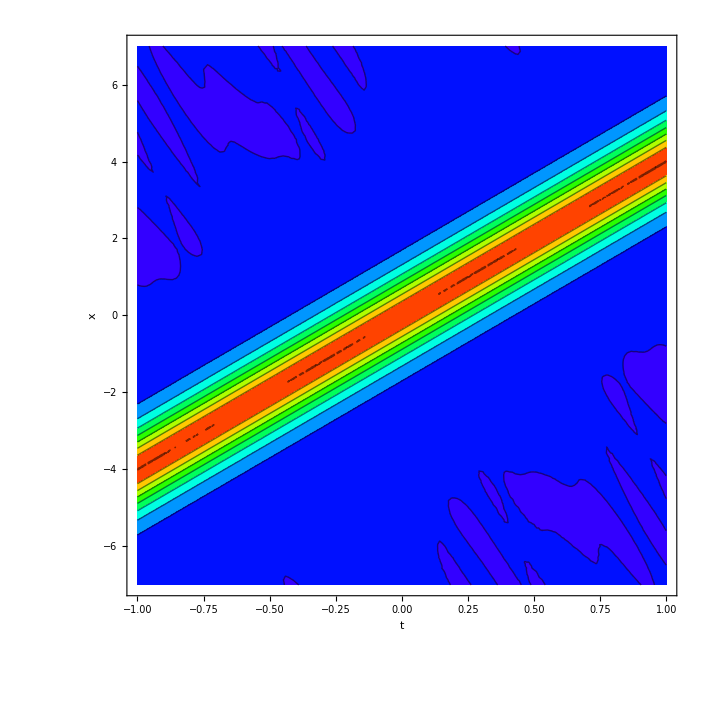

```mathematica
ContourPlot[u[x,t]/.Flatten[sol],{t,-1,1},{x,-7,7},
ColorFunction-> (Hue[0.7 #1]&),PlotPoints -> 50,PlotRange -> All,FrameLabel -> {"t","x"}]
```

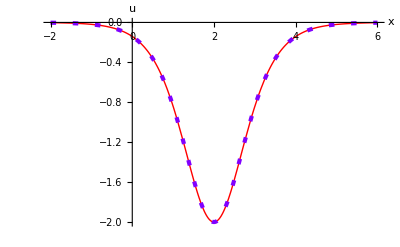

```mathematica
Plot[{u[x,0.5]/.Flatten[sol],-2 Sech[x-2]^2},
{x,-2,6},PlotStyle-> {{Hue[0],AbsoluteThickness[1]},
{Hue[0.75],Dashing[{0.01,0.03}],AbsoluteThickness[3]}},AxesLabel ->  {"x","u"}]
```

```mathematica
uexact[x_,t_]=-12(3+4 Cosh[2 x-8 t]+Cosh[4 x-64 t])/(3 Cosh[x-28 t]+Cosh[3 x-36 t])^2
```

-(12 (3+Cosh[64 t-4 x]+4 Cosh[8 t-2 x]))/(Cosh[36 t-3 x]+3 Cosh[28 t-x])^2

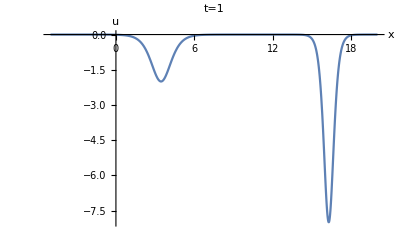

```mathematica
Plot[uexact[x,1],{x,-5,20}, PlotRange ->  All,PlotLabel-> "t=1",AxesLabel -> {"x","u"}]
```

```mathematica
Plot3D[uexact[x,t],{t,-0.3,0.3},{x,-6,6},PlotPoints ->  50,
PlotRange-> {-10,0},AxesLabel-> {"t","x","u"},ViewPoint->{-1.78,-2.06,2.5}]
```

-Graphics3D-

```mathematica
ContourPlot[uexact[x,t],{t,-1,1},{x,-12,12},
PlotPoints->  100,FrameLabel ->  {"t","x"},ColorFunction->  (Hue[0.7 #1]&),
PlotRange ->  All,Contours->  {-0.1,-0.6,-1.1,-1.6,-2.6,-4.,-5.6}]
```

-Graphics-

```mathematica
Animate[Plot[uexact[x,t],{x,-20,20},PlotRange-> {-9,0}],{t,-1,1,0.02}]
```

```mathematica
xmin=-12;xmax=12;
sol=NDSolve[{D[u[x,t],t] == 6 u[x,t] D[u[x,t],x]-D[u[x,t],{x,3}],
u[x,0] ==.8a-4 Sech[x]^2,u[xmin,t]== u[xmax,t]},u,{x,xmin,xmax},{t,0,1}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{u^(0,1)[x,t]==6 u[x,t] u^(1,0)[x,t]-u^(3,0)[x,t],u[x,0]==.8a-4 Sech[x]^2,u[-12,t]==u[12,t]},u,{x,-12,12},{t,0,1}]

```mathematica
Plot3D[u[x,t]/.Flatten[sol],{x,-10,10},{t,0,1},
PlotPoints-> 50,PlotRange-> All,AxesLabel-> {"x","t","u"}]
```

NDSolve::dsvar: -9.99959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{u^(0,1)[-9.99959,0.0000204286]==6 u[-9.99959,0.0000204286] u^(1,0)[-9.99959,0.0000204286]-u^(3,0)[-9.99959,0.0000204286],u[-9.99959,0]==-3.30054×10^-8+.8a,u[-12,0.0000204286]==u[12,0.0000204286]},u,{-9.99959,-12,12},{0.0000204286,0,1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -9.99959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{u^(0,1)[-9.99959,0.0000204286]==6. u[-9.99959,0.0000204286] u^(1,0)[-9.99959,0.0000204286]-1. u^(3,0)[-9.99959,0.0000204286],u[-9.99959,0.]==-3.30054×10^-8+.8a,u[-12.,0.0000204286]==u[12.,0.0000204286]},u,{-9.99959,-12.,12.},{0.0000204286,0.,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -9.59143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{u^(0,1)[-9.59143,0.0000204286]==6 u[-9.59143,0.0000204286] u^(1,0)[-9.59143,0.0000204286]-u^(3,0)[-9.59143,0.0000204286],u[-9.59143,0]==-7.4664×10^-8+.8a,u[-12,0.0000204286]==u[12,0.0000204286]},u,{-9.59143,-12,12},{0.0000204286,0,1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
Animate[Plot[u[x,t] /. Flatten[sol],{x,-5,10},PlotRange->  {-6,0}],{t,0,0.8,0.01}]
```